```mathematica
RandomFunction[WienerProcess[],{1,10,.1}]
```

TemporalData[…]

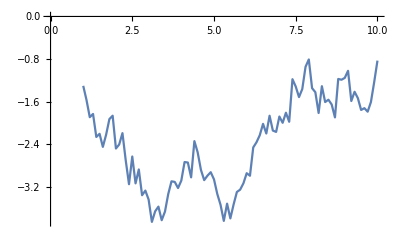

```mathematica
ListLinePlot[%1]
```

```mathematica
ListLinePlot[-Out[2]["Values"]]
```

ListLinePlot::lpn: -1. ()[Values] is not a list of numbers or pairs of numbers.

ListLinePlot[-(-Graphics-)[Values]]

```mathematica
-Out[2]["Values"]
```

-(-Graphics-)[Values]

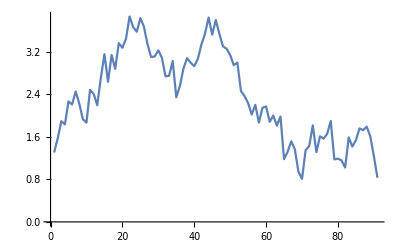

```mathematica
ListLinePlot[-Out[1]["Values"]]
```

```mathematica
ListLinePlot[Abs[Out[1]["Values"]]]
```

-Graphics-

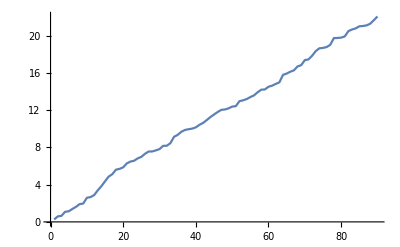

```mathematica
ListLinePlot[Accumulate[Abs[Differences@Out[1]["Values"]]]]
```

```mathematica
Min@Out[1]["Values"]
```

-3.86081

```mathematica
Max@Out[1]["Values"]
```

-0.807975

```mathematica
Accumulate[Abs[Differences@Out[1]["Values"]]]
```

{0.265753,0.588929,0.649448,1.08183,1.14091,1.38646,1.61505,1.90838,1.97225,2.58863,2.66483,2.87737,3.38963,3.83688,4.35742,4.86203,5.12307,5.60706,5.6939,5.86198,6.28211,6.48131,6.56916,6.82455,6.98598,7.31575,7.55582,7.56769,7.68221,7.82182,8.17079,8.18042,8.45863,9.13899,9.34845,9.67796,9.87167,9.95545,10.0206,10.1561,10.4284,10.6334,10.9354,11.2587,11.5355,11.7986,12.0323,12.0761,12.1955,12.3849,12.4323,12.9639,13.0614,13.1939,13.4073,13.5885,13.9224,14.2005,14.2266,14.5157,14.6333,14.8226,14.9931,15.794,15.9324,16.1303,16.2808,16.6989,16.8373,17.3767,17.4529,17.8436,18.3473,18.6451,18.689,18.7793,19.0212,19.7436,19.7583,19.7927,19.9257,20.4933,20.6672,20.7862,21.0089,21.0425,21.1084,21.2896,21.6645,22.0681}

```mathematica
Min[FinancialData["^SPX","Close",All]["Values"]]
```

16.66

```mathematica
Max[FinancialData["^SPX","Close",All]["Values"]]
```

3025.86

```mathematica
Max[FinancialData["^SPX","Close",All]["Values"]]/Min[FinancialData["^SPX","Close",All]["Values"]]
```

181.624

```mathematica
PercentForm[Out[13]]
```

18162%

```mathematica
ListLinePlot[Accumulate[Abs[Differences@FinancialData["^SPX","Close",All]["Values"]["Values"]]]]
```

StructuredArray::nosprop: Values is not in the list {Flattening,Magnitudes,Properties,Structure,StructuredAlgorithms,StructuredData,StructureSymbol,Summary,UnitBlock} of valid properties for QuantityArray StructuredArray objects.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[«1»].

StructuredArray::nosprop: Values is not in the list {Flattening,Magnitudes,Properties,Structure,StructuredAlgorithms,StructuredData,StructureSymbol,Summary,UnitBlock} of valid properties for QuantityArray StructuredArray objects.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[«1»].

StructuredArray::nosprop: Values is not in the list {Flattening,Magnitudes,Properties,Structure,StructuredAlgorithms,StructuredData,StructureSymbol,Summary,UnitBlock} of valid properties for QuantityArray StructuredArray objects.

General::stop: Further output of StructuredArray::nosprop will be suppressed during this calculation.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[«1»].

General::stop: Further output of Differences::listrp will be suppressed during this calculation.

ListLinePlot::lpn: Abs[Differences[«1»]] is not a list of numbers or pairs of numbers.

ListLinePlot[Abs[Differences[QuantityArray[…][Values]]]]

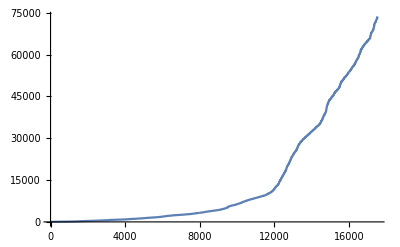

```mathematica
ListLinePlot[Accumulate[Abs[Differences@FinancialData["^SPX","Close",All]["Values"]]]]
```

```mathematica
Quantity[100,"USDollars"](Max[FinancialData["^SPX","Close",All]["Values"]]-Min[FinancialData["^SPX","Close",All]["Values"]])
```

300 920.01 $

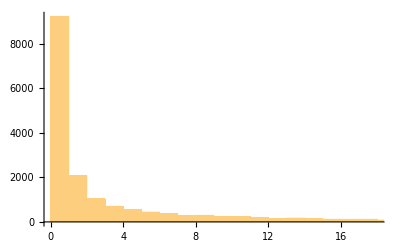

```mathematica
Histogram[Abs[Differences@FinancialData["^SPX","Close",All]["Values"]]]
```

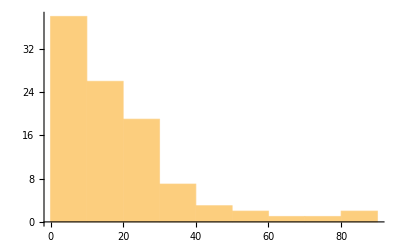

```mathematica
Histogram[Abs[Differences@FinancialData["^SPX","Close",All]["Values"][[-100;;]]]]
```

```mathematica
DiscreteWaveletTransform[Abs[Differences@FinancialData["^SPX","Close",All]["Values"][[-100;;]]]]
```

DiscreteWaveletData[<<DWT>>, <7>, {99}]

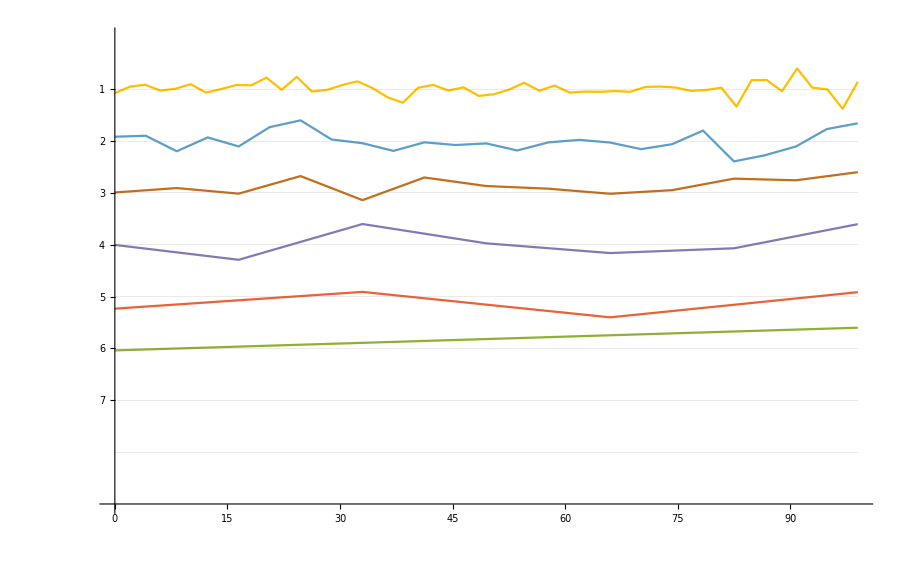

```mathematica
WaveletListPlot[%20]
```

```mathematica
ListLinePlot[Accumulate[Abs[Differences@FinancialData["NASDAQ:AAPL","Close",All]["Values"]]]]
```

$Aborted

```mathematica
Accumulate[Abs[Differences@FinancialData["NASDAQ:AAPL","Close",All]["Values"]]]
```

$Aborted

```mathematica
Differences@FinancialData["NASDAQ:AAPL","Close",All]["Values"]
```

{-0.03 $,-0.04 $,0.01 $,0.01 $,0.03 $,0.02 $,0.02 $,0.03 $,0.05 $,0.01 $,-0.02 $,-0.02 $,0.01 $,-0.01 $,-0.03 $,-0.02 $,-0.01 $,0.03 $,-0.00 $,-0.02 $,0.00 $,0.01 $,-0.00 $,0.03 $,-0.02 $,0.01 $,0.01 $,-0.00 $,-0.01 $,-0.00 $,-0.02 $,-0.02 $,-0.03 $,-0.03 $,0.02 $,0.02 $,0.00 $,0.00 $,-0.03 $,0.00 $,-0.02 $,-0.00 $,-0.01 $,0.01 $,0.02 $,-0.03 $,-0.02 $,0.01 $,-0.02 $,0.03 $,0.01 $,0.02 $,0.00 $,-0.01 $,-0.00 $,-0.00 $,-0.00 $,-0.04 $,-0.02 $,-0.02 $,0.02 $,-0.00 $,0.02 $,0.02 $,0.03 $,-0.00 $,0.00 $,0.02 $,-0.00 $,-0.01 $,-0.01 $,-0.02 $,0.00 $,-0.00 $,-0.00 $,0.04 $,0.00 $,-0.01 $,-0.00 $,0.02 $,0.01 $,0.01 $,0.00 $,0.00 $,-0.02 $,-0.03 $,0.00 $,0.01 $,0.03 $,0.02 $,0.01 $,-0.00 $,-0.00 $,-0.01 $,-0.01 $,0.01 $,0.00 $,-0.00 $,-0.00 $,-0.01 $,0.01 $,0.00 $,-0.01 $,0.00 $,-0.00 $,-0.01 $,0.01 $,0.01 $,-0.01 $,0.02 $,0.03 $,0.02 $,-0.00 $,0.03 $,0.00 $,0.00 $,0.00 $,-0.03 $,0.00 $,0.01 $,-0.01 $,-0.02 $,0.01 $,0.01 $,0.02 $,-0.01 $,-0.00 $,-0.01 $,-0.01 $,-0.00 $,-0.02 $,-0.02 $,0.01 $,-0.01 $,0.01 $,-0.01 $,-0.02 $,-0.04 $,-0.00 $,0.00 $,-0.02 $,0.00 $,0.02 $,-0.04 $,-0.03 $,0.01 $,0.02 $,0.01 $,0.01 $,0.02 $,-0.03 $,-0.00 $,-0.02 $,0.01 $,0.01 $,0.02 $,-0.02 $,-0.01 $,0.02 $,0.01 $,-0.00 $,0.01 $,0.01 $,-0.01 $,0.00 $,-0.00 $,-0.01 $,-0.01 $,-0.01 $,-0.01 $,-0.01 $,-0.01 $,-0.00 $,0.00 $,-0.03 $,-0.02 $,0.01 $,-0.01 $,0.00 $,0.02 $,0.00 $,0.02 $,0.01 $,-0.02 $,-0.00 $,-0.01 $,0.00 $,0.00 $,-0.00 $,-0.01 $,-0.01 $,-0.01 $,-0.01 $,0.00 $,0.00 $,-0.02 $,-0.01 $,-0.00 $,-0.04 $,0.00 $,0.01 $,0.00 $,0.00 $,0.02 $,0.01 $,-0.00 $,0.02 $,0.01 $,0.00 $,0.01 $,0.00 $,-0.02 $,0.01 $,-0.00 $,0.01 $,0.02 $,0.00 $,-0.00 $,-0.01 $,0.00 $,0.01 $,0.01 $,-0.00 $,0.00 $,0.00 $,-0.00 $,-0.01 $,-0.02 $,0.00 $,0.00 $,0.00 $,0.01 $,0.01 $,-0.02 $,-0.00 $,0.01 $,0.01 $,0.00 $,0.00 $,-0.02 $,-0.00 $,0.01 $,0.01 $,-0.00 $,0.00 $,0.00 $,-0.00 $,0.01 $,0.00 $,-0.01 $,0.00 $,0.00 $,-0.00 $,-0.01 $,0.01 $,0.02 $,0.03 $,0.03 $,-0.02 $,0.01 $,-0.01 $,0.00 $,-0.02 $,9335,10.34 $,-1.02 $,0.08 $,1.51 $,0.18 $,-15.73 $,6.07 $,-0.33 $,2.82 $,2.56 $,0.49 $,-1.51 $,-2.29 $,3.07 $,1.87 $,0.92 $,0.96 $,-3.52 $,0.62 $,-1.22 $,5.06 $,-1.46 $,-1.62 $,10.57 $,1.19 $,0.08 $,4.73 $,2.93 $,0.06 $,-3.30 $,-0.53 $,-0.98 $,1.46 $,-0.71 $,0.62 $,-0.38 $,0.51 $,1.10 $,-0.97 $,1.91 $,1.26 $,0.10 $,0.54 $,-1.72 $,1.82 $,0.88 $,-0.32 $,-1.01 $,-1.61 $,5.99 $,2.01 $,0.80 $,2.02 $,2.39 $,1.90 $,-1.49 $,1.63 $,6.93 $,-4.04 $,-2.31 $,-1.95 $,1.68 $,0.25 $,1.23 $,1.29 $,2.78 $,1.33 $,0.34 $,1.31 $,3.10 $,-0.60 $,1.12 $,-1.67 $,-0.08 $,0.36 $,0.02 $,3.88 $,0.73 $,0.67 $,2.95 $,-0.32 $,-1.88 $,-0.98 $,0.31 $,-3.94 $,9.85 $,-1.37 $,2.60 $,-3.27 $,-5.62 $,0.04 $,-2.18 $,-3.54 $,-11.46 $,2.94 $,2.26 $,-0.84 $,-1.08 $,-5.91 $,3.51 $,-3.82 $,-3.12 $,-0.69 $,-0.74 $,-0.85 $,0.92 $,-3.23 $,-1.77 $,6.34 $,2.90 $,2.68 $,4.93 $,2.43 $,2.23 $,-0.62 $,-0.04 $,-1.41 $,1.15 $,4.56 $,-0.58 $,1.59 $,-0.68 $,-0.20 $,-3.01 $,4.23 $,-0.06 $,-1.82 $,3.63 $,1.18 $,1.68 $,-0.18 $,-4.21 $,1.22 $,1.99 $,-1.48 $,1.55 $,1.91 $,-0.71 $,-1.15 $,2.31 $,-3.07 $,4.63 $,1.62 $,-0.17 $,-1.65 $,0.72 $,1.94 $,-0.90 $,4.26 $,-4.61 $,-4.41 $,-10.68 $,3.66 $,2.04 $,4.39 $,-2.44 $,-0.51 $,8.49 $,-6.22 $,-1.01 $,4.76 $,3.85 $,0.01 $,2.28 $,-0.18 $,-9.82 $,3.85 $,-2.33 $,1.37 $,3.48 $,-0.27 $,-3.04 $,3.49 $,4.09 $,-0.02 $,0.91 $,2.53 $,6.89 $,-0.50 $,-4.34 $,1.15 $,0.80 $,2.07 $,-1.81 $,-3.23 $,0.99 $,-1.04 $,3.35 $,-1.14 $,-1.07 $,5.15 $,0.62 $,-5.63 $,1.86 $,6.19 $,0.05 $,-2.66 $,2.63 $,3.06 $,6.12 $,-0.34 $,-0.55 $,-0.95 $,0.91 $,1.13 $,4.10 $,-0.55 $,3.22 $,0.40 $,3.00 $,2.47 $,-5.76 $,-0.03 $,5.50 $,7.06 $,1.68 $,-0.37 $,0.11 $,2.19 $,0.71 $,2.06 $,-0.24 $,2.51 $,-1.83 $,3.12 $,1.34 $,-0.81 $,-3.10 $,-1.18 $,-0.23 $,4.59 $,-2.08 $,3.55 $,-0.59 $,-3.09 $,-4.71 $,2.29 $,3.84 $,5.13 $,-3.79 $,1.56 $,2.29 $,0.69 $,3.69 $,4.71 $,0.55 $,-0.67 $,0.28 $,-0.58 $,4.56 $,0.27 $,5.64 $,-0.11 $,1.72 $,2.13 $,6.70 $,-2.92 $,2.37 $,-1.41 $,4.80 $,6.44 $,0.70 $,6.63 $}
 |  |  |  |

```mathematica
Map[QuantityMagnitude,Out[24]]
```

{-0.026786,-0.035714,0.011157,0.0134,0.029014,0.024557,0.022314,0.029015,0.053571,0.00892901,-0.015615,-0.017857,0.00668597,9835,0.269989,5.64001,-0.110016,1.72,2.13,6.70001,-2.92001,2.37,-1.40997,4.79999,6.44,0.699982,6.63}
 |  |  |  |

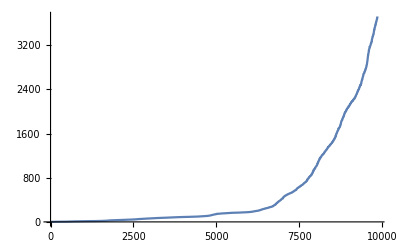

```mathematica
ListLinePlot[Accumulate[Abs[Differences[Map[QuantityMagnitude,FinancialData["NASDAQ:AAPL","Close",All]["Values"]]]]]]
```

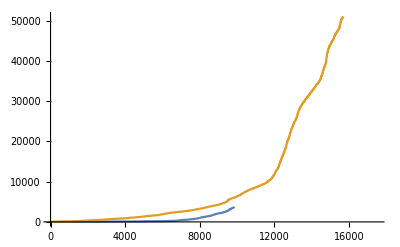

```mathematica
ListLinePlot[{
Accumulate[Abs[Differences[Map[QuantityMagnitude,FinancialData["NASDAQ:AAPL","Close",All]["Values"]]]]],
Accumulate[Abs[Differences@FinancialData["^SPX","Close",All]["Values"]]]
}]
```